## A366630: a(n) = phi(6^n + 1), where phi is Euler’s totient function (A000010).

### MATHEMATICA PROGRAM:

```mathematica
EulerPhi[6^Range[0,22]+1] (* Paul F.Marrero Romero, Oct 17 2023 *)
```

{1,6,36,180,1296,6000,41472,230496,1580800,8359200,58579200,310968900,2175102720,10971642240,76065091200,351048600000,2811459796992,14508487949472,88870766837760,522016066337712,3564233663616000,17479898551382400,128060205344805888}

### Formula:

a(n) = A000010(A062394(n)).  - Paul F. Marrero Romero, Oct 17 2023

### Plot section:

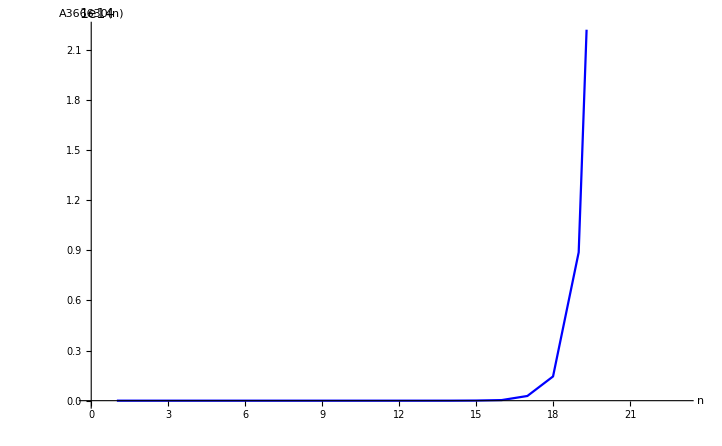

```mathematica
ListPlot[EulerPhi[6^Range[0,22]+1], Joined->True, PlotStyle->Blue, AxesLabel->{"n", "A366630(n)"}, LabelStyle->Directive [Black, Bold]]
```

### References:

Sean A. Irvine, a(n) = phi(6^n+1), where phi is Euler’s totient function (A000010), Entry A366630 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366630